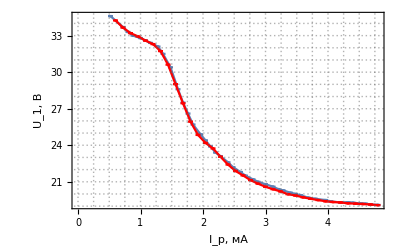

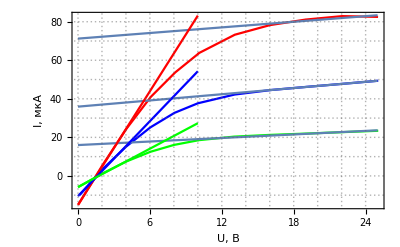

I_p, мА | 5 | 3 | 1.5
I_iH, мкА | 71.2329 | 35.9382 | 16.0041
σI_iH, мкА | 3.60327 | 0.0667763 | 0.597325
dI/dU_0, мкА/В | 9.81311 | 6.4767 | 3.30975
σdI/dU_0, мкА/В | 0.207326 | 0.314639 | 0.10865

I_p, мА | 5 | 3 | 1.5
kT_e, эВ | 3.62947 | 2.77442 | 2.41772
σkT_e, эВ | 0.198965 | 0.13488 | 0.120174
n_e, м^-3 | 6.04068×10^16 | 3.48576×10^16 | 1.66286×10^16
σn_e, м^-3 | 3.4754×10^15 | 8.49783×10^14 | 7.45638×10^14

I_p, мА | 5 | 3 | 1.5
kT_e, эВ | 3.62947 | 2.77442 | 2.41772
σkT_e, эВ | 0.198965 | 0.13488 | 0.120174
n_e, м^-3 | 6.04068×10^16 | 3.48576×10^16 | 1.66286×10^16
σn_e, м^-3 | 3.4754×10^15 | 8.49783×10^14 | 7.45638×10^14

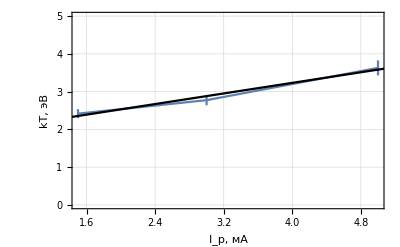

-Graphics-

1.38×10^-23

I_p, мА | 5 | 3 | 1.5
ω_p, c^-1 | 1.3857×10^10 | 1.05263×10^10 | 7.27035×10^9
σω_p, c^-1 | 3.9862×10^8 | 1.28309×10^8 | 1.63004×10^8
r_D, м | 4.86753×10^-6 | 6.40772×10^-6 | 9.27735×10^-6
σr_D, м | 1.40022×10^-7 | 7.81061×10^-8 | 2.08002×10^-7
N_D | 29.1811 | 38.4145 | 55.6181
σN_D | 0 | 0 | 0

```mathematica
Needs["ErrorBarPlots`"]
(*Diameter and Length Parameters*)
d=0.2;
l=5.2;
data1 = ({{34.6, 33.7, 33.3, 33, 32.8, 32.6, 32.4, 32.1, 31.5, 30.4, 28.6, 27.5, 26.6, 25.7, 24.9, 24.4, 23.9, 23.4, 23.1, 22.6, 22.2, 21.8, 21.5, 21.2, 21, 20.8, 20.6, 20.4, 20.3, 20.1, 20, 19.9, 19.7, 19.6, 19.5, 19.4, 19.3, 19.32, 19.28, 19.23, 19.2, 19.15, 19.1}, {13, 18, 20, 22, 25, 27, 29, 32, 34, 37, 40, 42, 44, 46, 49, 51, 53, 55, 57, 60, 62, 65, 67, 70, 72, 75, 78, 80, 82, 85, 87, 89, 92, 95, 99, 101, 105, 108, 110, 113, 115, 117, 120}});
data1Graph =data1;
data1Print = data1;
data1Print = ArrayPad[data1Print,{{0,1},{0,0}}];
For[i = 1, i≤43,i++,
data1Graph[[2,i]]=data1Graph[[2,i]]*6/150;
data1Print [[3,i]] = N[data1Graph[[2,i]]];
]
data1Print=ArrayPad[data1Print,{{0,0},{1,0}}];
data1Print[[1,1]]="U_1, В";
data1Print[[2,1]]="I_p, дел";
data1Print[[3,1]]="I_p, мА";
Export["3.5.1 Table 1.xlsx", data1Print];
data2  = ({{19.084, 19.134, 19.176, 19.203, 19.236, 19.304, 19.339, 19.402, 19.5, 19.608, 19.726, 19.875, 19.981, 20.209, 20.392, 20.590, 20.846, 21.134, 21.523, 21.888, 22.414, 23.054, 23.740, 24.191, 24.848, 25.937, 27.445, 29.016, 30.615, 31.729, 32.304, 32.589, 32.937, 33.205, 33.656, 34.245, 35.046}, {120, 117, 114, 111, 108, 105, 102, 99, 96, 93, 90, 87, 84, 81, 78, 75, 72, 69, 66, 63, 60, 57, 54, 51, 48, 45, 42, 39, 36, 33, 30, 27, 24, 21, 18, 15, 12}});
data2Graph = data2;
data2Print = data2;
data2Print = ArrayPad[data2Print,{{0,1},{0,0}}];
For[i = 1, i≤37,i++,
data2Graph[[2,i]] = data2Graph[[2,i]]*6/150;
data2Print[[3,i]] = N[data2Graph[[2,i]]];
]
data2Print = ArrayPad[data2Print,{{0,0},{1,0}}];
data2Print[[1,1]]="U_1, В";
data2Print[[2,1]]="I_p, дел";
data2Print[[3,1]]="I_p, мА";
Export["3.5.1 Table 2.xlsx", data2Print];
σIp = 0.04;
σU1 = 0.1;
IpErrors1 = Table[σIp, 43];
U1Errors1 = Table[σU1, 43];
IpErrors2 = Table[σIp,37];
U1Errors2 = Table[σU1,37];
Graph1ErrorValues1 = Table[0,43];
Graph1ErrorValues2 = Table[0,37];
For[i=1, i≤43, i++,
Graph1ErrorValues1[[i]] = ErrorBar[IpErrors1[[i]],U1Errors1[[i]]];
]
For[i=1,i<37,i++,
Graph1ErrorValues2[[i]]=ErrorBar[IpErrors2[[i]],U1Errors2[[i]]];
]
data1Graph=Transpose[data1Graph];
data2Graph=Transpose[data2Graph];
data1Graph=data1Graph.({{0, 1}, {1, 0}});
data2Graph=data2Graph.({{0, 1}, {1, 0}});
data1GraphLine = data1Graph;
data2GraphLine = data2Graph;
data1Graph=Partition[Riffle[data1Graph,Graph1ErrorValues1],2];
data2Graph=Partition[Riffle[data2Graph,Graph1ErrorValues2],2];
Show[ErrorListPlot[data1Graph, PlotRange->Automatic, PlotTheme->"Detailed", GridLines->All, Joined->True],ErrorListPlot[data2Graph,PlotRange->Automatic, PlotTheme->"Detailed", GridLines->All, Joined->True, PlotStyle->Red], FrameLabel->{{RawBoxes[RowBox[{"U_1, В"}]], None},{RawBoxes[RowBox[{"I_p, мА"}]],None}}, PlotLabel->None, LabelStyle->{FontFamily->"Times New Roman", GrayLevel[0]}, ImageSize->Full]

ex2Currents=({{5, 3, 1.5}});
ex2data1 = ({{82.51, 82.90, 81.11, 78.24, 73.25, 63.59, 63.43, 53.71, 41.08, 24.45, 5.44, -15.06}, {25.034, 22.042, 19.001, 16.017, 13.085, 10.048, 10.047, 8.115, 6.086, 4.0400, 2.0291, 0.0137}});
ex2data2= ({{49.37, 47.8, 46.19, 44.56, 42.21, 37.68, 32.72, 25.19, 15.19, 3.48, -9.95}, {25.047, 22.142, 19.071, 16.101, 13.066, 10.002, 8.052, 6.039, 4.0159, 2.0455, 0.136}});
ex2data3 = ({{23.42, 22.70, 21.95, 21.28, 20.37, 18.51, 18.46, 16.08, 12.53, 7.50, 1.18, -5.83}, {25.048, 22.018, 19.004, 16.026, 13.021, 10.014, 10.013, 8.012, 6.051, 4.0401, 2.0163, 0.013}});
ex2data1Print = ex2data1;
ex2data2Print = ex2data2;
ex2data3Print = ex2data3;
ex2data1Print = ArrayPad[ex2data1Print, {0,0},{1,0}];
ex2data2Print = ArrayPad[ex2data2Print, {0,0},{1,0}];
ex2data3Print = ArrayPad[ex2data3Print, {0,0},{1,0}];
ex2data1Print[[1,1]]="I, мкА";
ex2data2Print[[1,1]]="I, мкА";
ex2data3Print[[1,1]]="I, мкА";

ex2data1Print[[2,1]]="U, В";
ex2data2Print[[2,1]]="U, В";
ex2data3Print[[2,1]]="U, В";

Export["3.5.1 Experiment 2, 5.xlsx", Grid[ex2data1Print, Frame->All]];
Export["3.5.1 Experiment 2, 3.xlsx", Grid[ex2data2Print, Frame->All]];
Export["3.5.1 Experiment 2, 1,5.xlsx", Grid[ex2data3Print, Frame->All]];

ex2data1Graph = Transpose[ex2data1].({{0, 1}, {1, 0}});
ex2data2Graph = Transpose[ex2data2].({{0, 1}, {1, 0}});
ex2data3Graph = Transpose[ex2data3].({{0, 1}, {1, 0}});
ApproximationEx2data1 = LinearModelFit[ex2data1Graph[[1;;4]], x, x];
ApproximationEx2data2 = LinearModelFit[ex2data2Graph[[1;;4]], x, x];
ApproximationEx2data3 = LinearModelFit[ex2data3Graph[[1;;6]], x, x];
Normal[ApproximationEx2data1];
Normal[ApproximationEx2data2];
Normal[ApproximationEx2data3];
ApproximationEx2data1ZeroU = LinearModelFit[ex2data1Graph[[10;;12]],x,x];
ApproximationEx2data2ZeroU = LinearModelFit[ex2data2Graph[[9;;11]],x,x];
ApproximationEx2data3ZeroU = LinearModelFit[ex2data3Graph[[10;;12]],x,x];
Normal[ApproximationEx2data1ZeroU];
Normal[ApproximationEx2data2ZeroU];
Normal[ApproximationEx2data3ZeroU];
ex2data1Errors = Table[0,12];
ex2data2Errors = Table[0,11];
ex2data3Errors = Table[0,12];
For[i = 1, i≤12,i++,
ex2data1Errors[[i]]=ErrorBar[ex2data1Graph[[i,1]]*0.00012,ex2data1Graph[[i,2]]*0.00012];
ex2data3Errors[[i]]=ErrorBar[ex2data3Graph[[i,1]]*0.00012,ex2data3Graph[[i,2]]*0.00012];
]
For[i = 1, i<12,i++,
ex2data2Errors[[i]]=ErrorBar[ex2data2Graph[[i,1]]*0.00012, ex2data2Graph[[i,2]]*0.00012];
]
ex2data1Graph=Partition[Riffle[ex2data1Graph,ex2data1Errors],2];
ex2data2Graph=Partition[Riffle[ex2data2Graph,ex2data2Errors],2];
ex2data3Graph=Partition[Riffle[ex2data3Graph,ex2data3Errors],2];
Export["ex2data1Approximation.pdf",ApproximationEx2data1["ParameterTable"]];
Export["ex2data2Approximation.pdf",ApproximationEx2data2["ParameterTable"]];
Export["ex2data3Approximation.pdf",ApproximationEx2data3["ParameterTable"]];
Export["ex2data1ApproximationZeroU.pdf",ApproximationEx2data1ZeroU["ParameterTable"]];
Export["ex2data2ApproximationZeroU.pdf",ApproximationEx2data2ZeroU["ParameterTable"]];
Export["ex2data3ApproximationZeroU.pdf",ApproximationEx2data3ZeroU["ParameterTable"]];
ex2GraphData = Table[0,{i,5},{j,3}];
Show[ErrorListPlot[ex2data1Graph, PlotStyle->Red, PlotTheme->"Detailed", GridLines->All, Joined->True],ErrorListPlot[ex2data2Graph, PlotStyle->Blue,Joined->True],ErrorListPlot[ex2data3Graph,PlotStyle->Green,Joined->True], Plot[ApproximationEx2data1[x],{x, 0,25}], Plot[ApproximationEx2data2[x], {x, 0, 25}], Plot[ApproximationEx2data3[x], {x,0,25}],
Plot[ApproximationEx2data1ZeroU[x],{x,0,10},PlotStyle->Red],Plot[ApproximationEx2data2ZeroU[x],{x,0,10},PlotStyle->Blue],Plot[ApproximationEx2data3ZeroU[x],{x,0,10},PlotStyle->Green],
FrameLabel->{{RawBoxes[RowBox[{"I, мкА"}]], None},{RawBoxes[RowBox[{"U, В"}]],None}}, PlotLabel->None, LabelStyle->{FontFamily->"Times New Roman", GrayLevel[0]}, ImageSize->Full]
For[i=1,i≤3,i++,
ex2GraphData[[1,i]]=ex2Currents[[1,i]];
]
ex2GraphData[[2,1]]=ApproximationEx2data1["BestFitParameters"][[1]];
ex2GraphData[[2,2]]=ApproximationEx2data2["BestFitParameters"][[1]];
ex2GraphData[[2,3]]=ApproximationEx2data3["BestFitParameters"][[1]];

ex2GraphData[[3,1]]=ApproximationEx2data1["ParameterErrors"][[1]];
ex2GraphData[[3,2]]=ApproximationEx2data2["ParameterErrors"][[1]];
ex2GraphData[[3,3]]=ApproximationEx2data3["ParameterErrors"][[1]];

ex2GraphData[[4,1]]=ApproximationEx2data1ZeroU["BestFitParameters"][[2]];
ex2GraphData[[4,2]]=ApproximationEx2data2ZeroU["BestFitParameters"][[2]];
ex2GraphData[[4,3]]=ApproximationEx2data3ZeroU["BestFitParameters"][[2]];

ex2GraphData[[5,1]]=ApproximationEx2data1ZeroU["ParameterErrors"][[2]];
ex2GraphData[[5,2]]=ApproximationEx2data2ZeroU["ParameterErrors"][[2]];
ex2GraphData[[5,3]]=ApproximationEx2data3ZeroU["ParameterErrors"][[2]];

ex2GraphDataPrint=ex2GraphData;
ex2GraphDataPrint = ArrayPad[ex2GraphDataPrint,{{0,0},{1,0}}];
ex2GraphDataPrint[[1,1]] = "I_p, мА";
ex2GraphDataPrint[[2,1]] = "I_iH, мкА";
ex2GraphDataPrint[[3,1]] = "σI_iH, мкА";
ex2GraphDataPrint[[4,1]] = "dI/dU_0, мкА/В";
ex2GraphDataPrint[[5,1]] = "σdI/dU_0, мкА/В";
Grid[ex2GraphDataPrint, Frame->All]
Export["ex2Total.pdf", Grid[ex2GraphDataPrint, Frame->All]];
kTnGrid=Table[0,{i, 5},{j,3}];
kTe[Current_, DerivativeUI_]:=1/2*Current/DerivativeUI;
ne[Current_,mi_,e_,S_,kT_]:=(Current*10^-6*√mi)/(0.4*e*S*10^-6*√(2*kT*1.6*10^-19));
For[i=1,i≤3,i++,
kTnGrid[[1,i]]=ex2GraphData[[1,i]];
kTnGrid[[2,i]]=N[kTe[ex2GraphData[[2,i]], ex2GraphData[[4,i]]]];
kTnGrid[[3,i]]=N[Sqrt[
(D[kTe[Current,DerivativeUI],Current]/.DerivativeUI-> ex2GraphData[[4,i]])^2*ex2GraphData[[3,i]]^2+((D[kTe[Current,DerivativeUI],DerivativeUI]/.Current-> ex2GraphData[[2,i]])/.DerivativeUI->ex2GraphData[[4,i]])^2*
ex2GraphData[[5,i]]^2
]];
kTnGrid[[4,i]]=N[ne[ex2GraphData[[2,i]],22*1.66*10^-27,1.6*10^-19,d*l*Pi,kTnGrid[[2,i]]]];
kTnGrid[[5,i]]=N[Sqrt[
((D[ne[Current,22*1.66*10^-27,1.6*10^-19,d*l*Pi,kT],Current]/.Current-> ex2GraphData[[2,i]])/.kT->kTnGrid[[2,i]])^2*ex2GraphData[[3,i]]^2+
((D[ne[Current,22*1.66*10^-27,1.6*10^-19,d*l*Pi,kT],kT]/.Current->ex2GraphData[[2,i]])/.kT-> kTnGrid[[2,i]])^2*kTnGrid[[3,i]]^2
]
]]
kTnGridPrint=ArrayPad[kTnGrid,{{0,0},{1,0}}];
kTnGridPrint[[1,1]]="I_p, мА";
kTnGridPrint[[2,1]]="kT_e, эВ";
kTnGridPrint[[3,1]]="σkT_e, эВ";
kTnGridPrint[[4,1]]="n_e, (:043c)^-3";
kTnGridPrint[[5,1]]="σn_e, (:043c)^-3";
kTnGridPrint=Grid[kTnGridPrint,Frame->All]
Export["kTnGridPrint.pdf",kTnGridPrint];
kTnGridPrint
TIp=kTnGrid[[1;;2]];
TIpErrors = kTnGrid[[3]];
TIp=Transpose[TIp];
TIpApproximationLine = LinearModelFit[TIp,x,x];
For[i=1,i≤3,i++,
TIpErrors[[i]]=ErrorBar[0,TIpErrors[[i]]];
]
TIp=Partition[Riffle[TIp,TIpErrors],2];
Show[ErrorListPlot[TIp,PlotRange->{0,5}, PlotTheme->"Detailed", Joined->True], Plot[TIpApproximationLine[x],{x,0,6},PlotStyle->Black],
FrameLabel->{{RawBoxes[RowBox[{"kT, эВ"}]], None},{RawBoxes[RowBox[{"I_p, мА"}]],None}}, PlotLabel->None, LabelStyle->{FontFamily->"Times New Roman", GrayLevel[0]}]
nIp={kTnGrid[[1]],kTnGrid[[4]]};
nIpErrors=kTnGrid[[5]];
nIp=Transpose[nIp];
nIpApproximationLine=LinearModelFit[nIp,x,x];
For[i=1,i≤3,i++,
nIpErrors[[i]]=ErrorBar[0,nIpErrors[[i]]];
]
nIp=Partition[Riffle[nIp,nIpErrors],2];
Show[ErrorListPlot[nIp,PlotRange->Full,PlotTheme->"Detailed",Joined->True],Plot[nIpApproximationLine[x],{x,0,6},PlotStyle->Black],
FrameLabel->{{RawBoxes[RowBox[{"n*10^15, (:043c)^-3"}]], None},{RawBoxes[RowBox[{"I_p, мА"}]],None}}, PlotLabel->None, LabelStyle->{FontFamily->"Times New Roman", GrayLevel[0]}]
k=1.38*10^-23
me=0.91*10^-30;
ϵ=8.85×10^-12;
e=1.6*10^-19;
ωp[n_]:=√((n*e^2)/(ϵ*me)); 
rD[n_]:=√((ϵ*k*300)/(n*e^2));
Nd[n_,r_]:=n*4/3 π*r^3;
FinalResults ={kTnGrid[[1]],Table[0,3],Table[0,3],Table[0,3],Table[0,3],Table[0,3],Table[0,3]};
For[i=1,i≤3,i++,
FinalResults[[2,i]]=ωp[kTnGrid[[4,i]]];
FinalResults[[3,i]]=Sqrt[
(D[ωp[n],n]/.n->kTnGrid[[4,i]])^2*kTnGrid[[5,i]]^2
];
FinalResults[[4,i]]=rD[kTnGrid[[4,i]]];
FinalResults[[5,i]]=Sqrt[
(D[rD[n],n]/.n->kTnGrid[[4,i]])^2*kTnGrid[[5,i]]^2
];
FinalResults[[6,i]]=Nd[kTnGrid[[4,i]],FinalResults[[4,i]]];
]
FinalResultsPrint = ArrayPad[FinalResults, {{0,0},{1,0}}];
FinalResultsPrint[[1,1]]="I_p, мА";
FinalResultsPrint[[2,1]]="ω_p, c^-1";
FinalResultsPrint[[3,1]]="σω_p, c^-1";
FinalResultsPrint[[4,1]]="r_D, м";
FinalResultsPrint[[5,1]]="σr_D, м";
FinalResultsPrint[[6,1]]="N_D";
FinalResultsPrint[[7,1]]="σN_D";
Grid[FinalResultsPrint, Frame->All]

Export["FinalResults.pdf",Grid[FinalResultsPrint, Frame->All]];
```

```mathematica
100/(1.38*10^-23*300)
```

2.41546×10^22

```mathematica
Nd[6*10^16, 4.8*10^-6]
```

27.7948